```mathematica
f[x_]:=s Exp[-s *x]
```

```mathematica
s:= 2
```

```mathematica
Clear[s]
```

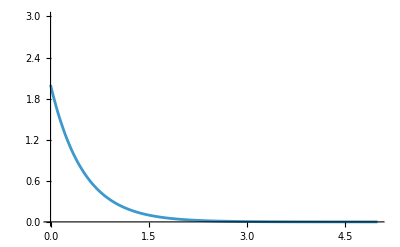

```mathematica
Plot[f[x],{x,0,5},PlotRange->{0,3}]
```

```mathematica
p[T_] := -1/s*Log[T/s]
```

```mathematica
μ[T_] := Integrate[x *f[x],{x,0,p[T]}]
```

```mathematica
V[T_] := Simplify[Integrate[x^2*f[x],{x,0,p[T]}]-μ[T]^2]
```

```mathematica
TotalVar[T_] :=p[T]*V[T]+p[T]*(1-p[T])*μ[T]^2
```

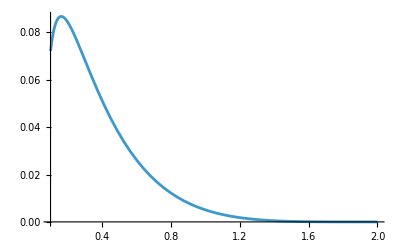

```mathematica
Plot[TotalVar[T],{T,0.1,2}]
```